# Recurrent Neural Networks

Sebastian Bodenstein
Wolfram Research
sebastianb@wolfram.com

## Outline

#### What are recurrent nets, and why are they interesting?

#### How to use recurrent nets

#### An application: integer addition

#### Advanced application: question answering

## The Problem

Try predict the next character in the sequence:

{W, h, y, “ “, a, r, e, “ “ , y, o, u, “ “, a, s, k, i, n}

The prediction method must have a notion of order: the exact order of the sequence matters!

Ordinary neural nets do not have any notion of order.

Solution: recurrent networks! (or RNNs)

## Why Recurrent Nets Are Interesting

### Lots of Applications

Speech Recognition

All state-of-the-art speech recognition systems make use of RNNs.

e.g., Baidu’s Deep Speech 2

https://arxiv.org/abs/1512.02595

Speech Synthesis

“Tacotron: Towards End-to-End Speech Synthesis”, Wang et al.

https://arxiv.org/abs/1703.10135

Cool demo: https://google.github.io/tacotron

Language Translation

Google Translate switched to using RNNs last year (their system: https://arxiv.org/abs/1609.08144).

“As dawn broke over Tokyo, Google Translate was the No. 1 trend on Japanese Twitter, just above some cult anime series and the long-awaited new single from a girl-idol supergroup. Everybody wondered: How had Google Translate become so uncannily artful?”: https://www.nytimes.com/2016/12/14/magazine/the-great-ai-awakening.html

## Why Recurrent Nets Are Interesting

### Lots of Applications

Image Caption Generation

Taken from: http://googleresearch.blogspot.com/2014/11/a-picture-is-worth-thousand-coherent.html

## Why Recurrent Nets Are Interesting

### Lots of Applications

Question Answering

An example from the Squad Dataset (https://rajpurkar.github.io/SQuAD-explorer):

Context:

One of the most famous people born in Warsaw was Maria Skłodowska-Curie, who achieved international recognition for her research on radioactivity and was the first female recipient of the Nobel Prize. Famous musicians include Władysław Szpilman and Frédéric Chopin. Though Chopin was born in the village of Żelazowa Wola, about 60 km (37 mi) from Warsaw, he moved to the city with his family when he was seven months old. Casimir Pulaski, a Polish general and hero of the American Revolutionary War, was born here in 1745.

Question:

What was Maria Curie the first female recipient of?

Prediction by Match-LSTM network:

Nobel Prize

Others

sentiment analysis

language modeling

time-series prediction

## Why Recurrent Nets Are Interesting

### They Are Arbitrarily Powerful Models

Theorem (Universal Approximation Theorem): NetChain[{DotPlusLayer[n], ElementwiseLayer[Tanh]}] can approximate any continuous function (on a compact subset of R^n) arbitrarily well for some finite number of neurons n.

Theorem: Recurrent neural networks are Turing complete (Siegelmann, H. T. and Sontag, E. D. 1995)

## What Is a Recurrent Network

Recurrent neural nets have feedback loops:

A feedback loop can be “unrolled”:

This is now a feedforward network with parameter sharing:

Taken from: http://colah.github.io/posts/2015-08-Understanding-LSTMs

## What is a Recurrent Network

RNNs are very simple to implement:

```mathematica
rnnTimeStep[params_Association,input_,state_]:=Tanh[params["StateWeights"].state+params["InputWeights"].input+params["Biases"]];
```

```mathematica
rnnLayerForward[params_Association,input_,state_]:=Rest@FoldList[rnnTimeStep[params,#2,#1]&,state,input]
```

Find the derivative function is harder, though.

A nice blog post exploring the link between functional programming and neural nets:

http://colah.github.io/posts/2015-09-NN-Types-FP

## What is a Recurrent Network

Let’s show that this is the same as BasicRecurrentLayer:

```mathematica
sequenceLength=3;
featureSize=2;
rnnStateSize=1;
inData=RandomReal[1,{sequenceLength,featureSize}];
state=ConstantArray[0,rnnStateSize];
```

Create a BasicRecurrentLayer and initialize it:

```mathematica
net=NetInitialize@BasicRecurrentLayer[rnnStateSize,"Input"->Dimensions@inData]
```

BasicRecurrentLayer[<>]

Extract its parameters:

```mathematica
param=NetExtract[net,"Arrays"]
```

<|InputWeights→{{-0.529935,-0.423679}},StateWeights→{{-1.61389}},Biases→{0.}|>

Evaluate the built-in Mathematica® implementation:

```mathematica
net[inData]
```

{{-0.232319},{0.286184},{-0.582591}}

Evaluate the implementation:

```mathematica
rnnLayerForward[param,inData,state]
```

{{-0.232319},{0.286184},{-0.582591}}

## What is a Recurrent Network

### What about LSTM’s, GRU’s, etc.?

Plain RNNs have traditionally been hard to train.

RNN == very deep feedforward network!

Exploding/vanishing gradients

```mathematica
<<NeuralNetworks`
```

NetChain[]

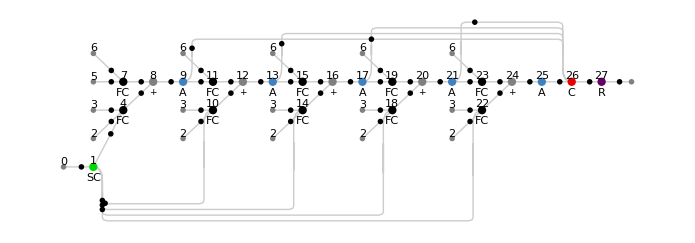

```mathematica
net=NetChain[{BasicRecurrentLayer[4]},"Input"->{"Varying",5}]
sequenceLen=5;
MXPlanPlot[net,sequenceLen]
```

#### For More:

Exploding/vanishing gradients problem was discovered by Sepp Hochreiter and described in his 1991 diploma thesis (“Untersuchungen zu dynamischen neuronalen Netzen,” Diploma thesis, TU Munich, 1991. http://people.idsia.ch/~juergen/SeppHochreiter1991ThesisAdvisorSchmidhuber.pdf.)

“On the Difficulty of Training Recurrent Neural Networks,” Pascanu et al. http://proceedings.mlr.press/v28/pascanu13.pdf.

## What Is a Recurrent Network?

### What about LSTM’s, GRU’s, etc.?

More complicated RNNs have been proposed to allow for simpler training.

Consider a BasicRecurrentLayer:

Now consider a LongShortTermMemoryLayer:

Taken from: http://colah.github.io/posts/2015-08-Understanding-LSTMs

Lots of variants (LSTM, GRU):

Define your own using NetFoldOperator!

## Example: Integer Addition

Generate training data:

```mathematica
makeRule[a_,b_]:=IntegerString[a]<>"+"<>IntegerString[b]->a+b;
trainingData=Flatten@Table[makeRule[i,j],{i,0,99},{j,0,99}];
RandomSample[trainingData,4]//InputForm
```

{"97+60" -> 157, "37+89" -> 126, "19+56" -> 75, 
 "27+29" -> 56}

```mathematica
"97+60"
```

Define a NetEncoder:

```mathematica
enc=NetEncoder[{"Characters",{DigitCharacter,"+"}}];
```

```mathematica
enc@"97+60+"
```

{10,8,11,7,1,11}

Define a net that takes a sequence of character inputs and predicts a number:

```mathematica
net=NetChain[{UnitVectorLayer[],LongShortTermMemoryLayer[40],LongShortTermMemoryLayer[20],SequenceLastLayer[],LinearLayer[]},"Input"->enc,"Output"->"Real"]
```

NetChain[]

## Example: Integer Addition (continued)

Train the net:

```mathematica
trained=NetTrain[net,trainingData,BatchSize->64,MaxTrainingRounds->200,ValidationSet->Scaled[0.1]]
```

NetChain[]

Evaluate on some examples:

```mathematica
trained[{"5+2","10+25","9+11","44+44"}]
```

{6.47626,35.1461,20.7937,88.0641}

## Example: Question Answering

Get the data:

```mathematica
ro=ResourceObject["The 20-Task bAbI Question-Answering Dataset v1.2"]
```

ResourceObject[…]

```mathematica
traindata=ResourceData[ro,"TrainingData"]["Task1"];
testdata=ResourceData[ro,"TestData"]["Task1"];
```

```mathematica
traindata[[All,100]]
```

<|Context→Mary went back to the bedroom. Mary travelled to the bathroom. John travelled to the office. Mary travelled to the bedroom. John journeyed to the kitchen. John moved to the hallway. Daniel moved to the hallway. Mary went back to the garden. Daniel went back to the office. Daniel travelled to the kitchen.,Question→Where is Daniel?,Answer→kitchen|>

## Example: Question Answering (continued)

Get all the words used:

```mathematica
dict=Union@@TextWords[Join[traindata["Context"],traindata["Question"]]]
```

{back,bathroom,bedroom,Daniel,garden,hallway,is,John,journeyed,kitchen,Mary,moved,office,Sandra,the,to,travelled,went,Where}

Get all the classes predicted:

```mathematica
classes=Union[traindata["Answer"]]
```

{bathroom,bedroom,garden,hallway,kitchen,office}

Create a NetEncoder for words:

```mathematica
enc=NetEncoder[{"Tokens",Join[dict,{"."}]}]
```

NetEncoder[<>]

## Example: Question Answering (continued)

Define a network taking a question and a context, and predict an answer:

```mathematica
net=NetGraph[<|
"context"->{EmbeddingLayer[50],DropoutLayer[0.3]},"question"->{EmbeddingLayer[50],DropoutLayer[0.3],LongShortTermMemoryLayer[50],SequenceLastLayer[]},
"cat"->CatenateLayer[],
"classifier"->{LongShortTermMemoryLayer[50],SequenceLastLayer[],DropoutLayer[0.3],LinearLayer[Length[classes]],SoftmaxLayer[]}|>,
{NetPort["Context"]->"context",NetPort["Question"]->"question",
{"question","context"}->"cat","cat"->"classifier"->NetPort["Answer"]},
"Context"->enc,"Question"->enc,"Answer"->NetDecoder[{"Class",classes}]]
```

NetGraph[]

## Example: Question Answering (continued)

Train the net:

```mathematica
trainedNet=NetTrain[net,traindata,ValidationSet->testdata,MaxTrainingRounds->15]
```

NetGraph[]

```mathematica
trainedNet[<|"Context"->"Sandra went to the office. Sandra travelled to the bathroom. Mary went back to the bedroom. Daniel moved to the garden. John journeyed to the garden. Daniel went back to the hallway. John journeyed to the bedroom. Mary travelled to the kitchen. Sandra went to the bedroom. Daniel went to the garden.","Question"->"Where is Daniel?"|>]
```

garden

Obtain the accuracy of the trained net on the test set:

```mathematica
N@Count[trainedNet[KeyDrop[testdata,"Answer"]]-testdata["Answer"],0]/Length[testdata["Answer"]]
```

0.527

## Going Further

More examples:

Documentation: NetTrain▶Applications▶Sequence Learning and NLP

Best book:

Bengio el al., Deep Learning, http://www.deeplearningbook.org/

Thorough section on RNNs

Best course:

CS224d: Deep Learning for Natural Language Processing, Stanford http://cs224d.stanford.edu/syllabus.html

Some fun blog posts:

“The Unreasonable Effectiveness of Recurrent Neural Networks”: http://karpathy.github.io/2015/05/21/rnn-effectiveness/

“Neural Networks, Types, and Functional Programming”: http://colah.github.io/posts/2015-09-NN-Types-FP

“Understanding LSTM Networks”: http://colah.github.io/posts/2015-08-Understanding-LSTMs/

“Attention and Augmented Recurrent Neural Networks”: http://distill.pub/2016/augmented-rnns/